# Упражнение 9. Метод на най-малките квадрати

### 1 зад. В таблицата са дадени данни за това как нивото на въглеродния диоксид в атмосферата се е изменяло в периода 1980-2000 "година" | 1980 | 1982 | 1984 | 1986 | 1988 | 1990 | 1992 | 1994 | 1996 | 1998 | 2000 "CO_2" | 338.7 | 341.1 | 344.4 | 347.2 | 351.5 | 354.2 | 356.4 | 358.9 | 362.6 | 366.6 | 369.4

### 2 зад. Топка е пусната от височина 450m. Нейната височина е измервана през интервали от 1 сек. и резултатите са поместени в таблицата "t, sec" | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 "h, m" | 450 | 445 | 431 | 408 | 375 | 332 | 279 | 216 | 143 | 61

### 3 зад. Следната таблица съдържа данни за това как се изменя броя на транзисторите в един процесор в хиляди в зависимост от годината: "година" | 1971 | 1972 | 1974 | 1978 | 1982 | 1985 | 1989 | 1993 | 1997 | 1999 | 2000 "бр.(x1000)" | 2.25 | 2.5 | 5 | 29 | 120 | 275 | 1180 | 3100 | 7500 | 24000 | 42000

```mathematica
(*Exercise 1 from whiteboard*)
```

```mathematica
nodes = {0, 1 ,2,3,4};
values= {1,2,1,0,4};
```

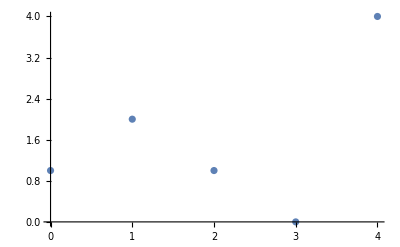
```mathematica
nodesPlot = ListPlot[Transpose[{nodes,values}]];
Show[nodesPlot]
-Graphics-
```

```mathematica
func[a_,b_] = Sum[(a*nodes[[i]]+b-values[[i]])^2,{i, 1,5}]; (*The finction ф that is the sum of the erros to the power of 2*)
func[a,b]
(-1+b)^2+(-2+a+b)^2+(-1+2 a+b)^2+(3 a+b)^2+(-4+4 a+b)^2
```

```mathematica
(*Finding the derivatives in order to find the a & b where the start function is closes to the nodes*)
DerivByA[a_, b_] = D[func[a,b], a]; 
DerivByB[a_,b_] = D[func[a,b],b];
```

```mathematica
DerivByA[a,b]
2 (-2+a+b)+4 (-1+2 a+b)+6 (3 a+b)+8 (-4+4 a+b)
DerivByB[a,b]
2 (-1+b)+2 (-2+a+b)+2 (-1+2 a+b)+2 (3 a+b)+2 (-4+4 a+b)
```

```mathematica
(*Solving the system of the derivatives by a & b. The result are the coeficients we are looking for (a & b)*)
coefs = Solve[{DerivByA[a,b] == 0, DerivByB[a,b]==0},{a,b}];
coefs
{{a->2/5,b->4/5}}
```

```mathematica
(*The function that we will substitute a & b in.*)
startFunction[x_] = a*x+b;
```

```mathematica
(*Substituting the values we found.*)
subst[x_]=startFunction[x] /.coefs[[1]];
subst[x]
4/5+(2 x)/5
```

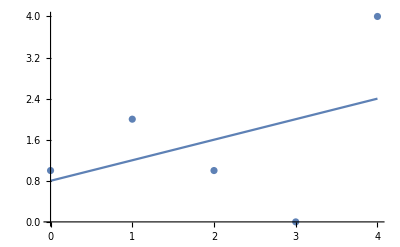
```mathematica
finalFuncPlot = Plot[subst[x], {x, 0,4}];
Show[{nodesPlot, finalFuncPlot}]
-Graphics-
```

```mathematica
(*Exercise 1*)
```

```mathematica
year = {1980,1982 ,1984,1986 ,1988 ,1990, 1992 ,1994, 1996,1998,2000};
Co2Values = {338.7,341.1,344.4,347.2,351.5,354.2,356.4,358.9,362.6,366.6,369.4};
```

```mathematica
baseLin [x_] = a*x+b;
linearFunc[a_,b_]= Sum[(a*year[[i]]+b-Co2Values[[i]])^2,{i, 1,Length[year]}];

linearFunc[a,b]
(-338.7+1980 a+b)^2+(-341.1+1982 a+b)^2+(-344.4+1984 a+b)^2+(-347.2+1986 a+b)^2+(-351.5+1988 a+b)^2+(-354.2+1990 a+b)^2+(-356.4+1992 a+b)^2+(-358.9+1994 a+b)^2+(-362.6+1996 a+b)^2+(-366.6+1998 a+b)^2+(-369.4+2000 a+b)^2
```

```mathematica
DerA[a_,b_] =D[linearFunc[a,b], a];
DerB[a_,b_] = D[linearFunc[a,b],b]; 
DerA[a,b]
3960 (-338.7+1980 a+b)+3964 (-341.1+1982 a+b)+3968 (-344.4+1984 a+b)+3972 (-347.2+1986 a+b)+3976 (-351.5+1988 a+b)+3980 (-354.2+1990 a+b)+3984 (-356.4+1992 a+b)+3988 (-358.9+1994 a+b)+3992 (-362.6+1996 a+b)+3996 (-366.6+1998 a+b)+4000 (-369.4+2000 a+b)
```

```mathematica
foundCoefs = Solve[{DerA[a,b]==0, DerB[a,b]==0},{a,b}];

foundCoefs
{{a->1.538181818167785,b->-2707.2545454266196}}
```

```mathematica
finalPoly[x_] = baseLin[x]/.foundCoefs;

finalPoly[x]
{-2707.2545454266196+1.538181818167785 x}
```

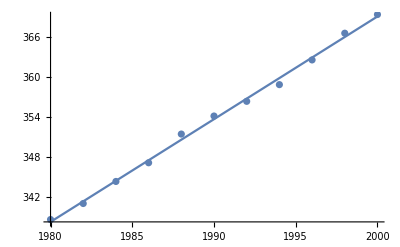
```mathematica
finalPolyPlot = Plot[finalPoly[x], {x, 1980, 2000}];
Co2NodesPlot=ListPlot[Transpose[{year, Co2Values}]];
Show[{finalPolyPlot,Co2NodesPlot}]

-Graphics-
```

```mathematica
(*Exercise 2*)
```

```mathematica
seconds={0,1,2,3,4,5,6,7,8,9};
height={450,445,431,408,375,332,279,216,143,61};
```

```mathematica
baseFunc[x_]=a x^2+b x+c; (*Here you can see that here I will use a quadratic function in order to more accuratelly approximate the function.*)
sumFunc[a_,b_,c_]=∑_(i=1)^Length[seconds] (a seconds⟦i⟧^2+b seconds⟦i⟧+c-height⟦i⟧)^2;
```

```mathematica
DerivativeA[a_,b_,c_]=D[sumFunc[a,b,c], a];
DerivativeB[a_,b_,c_]=D[sumFunc[a,b,c], b];
DerivativeC[a_,b_,c_]=D[sumFunc[a,b,c], c];
```

```mathematica
coefs=Solve[{DerivativeA[a,b,c]==0,DerivativeB[a,b,c]==0,DerivativeC[a,b,c]==0},{a,b,c}];

coefs
{{a->-647/132,b->127/132,c->4943/11}}
```

```mathematica
substituedBaseFunc[x_]=baseFunc[x]/.coefs⟦1⟧;

substituedBaseFunc[x]
4943/11+(127 x)/132-(647 x^2)/132
```

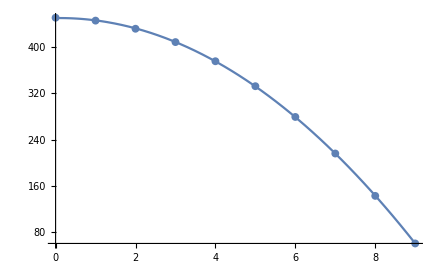
```mathematica
inputNodesPlot=ListPlot[Transpose[{seconds,height}]];
funcPlot=Plot[substituedBaseFunc[x],{x,0,9}];
Show[{funcPlot,inputNodesPlot}]
-Graphics-
```